# Useful functions

```mathematica
makeSystem[var_, vart_, sys_]:= Module[{v, vt, S, St, Sf},
v = var;
vt = vart;
S = sys;
(St = S/.Thread[v-> vt]; Sf = Thread[D[vt, t] == St])]
```

```mathematica
FollowRoot[system_,commonpars_,followPar_,range_,variables_, initialEq_]:=Module[{sys,cpar,fp, r,v,en, ieq, eq, pars, results},sys=system;cpar=commonpars;fp=followPar;r = range;v=variables;
ieq = initialEq;
results={};
Do[eq=ieq;
pars = Join[cpar, {fp-> i}];
ieq = FindRoot[Thread[sys == ConstantArray[0, Length[v]]]/.pars,Thread[{v, v/.ieq}]];
results = AppendTo[results, ieq], {i, range}];
results];
```

```mathematica
StableMark[jacobmatrix_, parcommon_, parfollow_, equilibrium_]:=
Module[{jmat, pc, pf, r,eq, eiv, anyZero, anyPos, allNeg},
jmat = jacobmatrix;
pc = parcommon;
pf = parfollow;
eq = equilibrium;
eiv = Eigenvalues[jmat/.pc/.pf/.eq];
anyZero = AnyTrue[Thread[-10^-10<=Re[eiv]<=10^-10], TrueQ];
anyPos = AnyTrue[Thread[Re[eiv]>10^-10], TrueQ];
allNeg = AllTrue[Thread[Re[eiv]<-10^-10], TrueQ];
Which[anyZero, "*",anyPos, "*", allNeg, "."]]
```

```mathematica
ListMark[jacobmatrix_, parcommon_, parfollow_, range_,equiList_]:=
Module[{jmat, pc, pf, r,eql, eiv},
jmat = jacobmatrix;
pc = parcommon;
pf = parfollow;
r=range;
eql = equiList;
MapThread[StableMark,{ConstantArray[jmat, Length[eql]], ConstantArray[pc, Length[eql]],Thread[pf->r], eql}]]
```

# Single infection

## Ecological dynamics of a resident

```mathematica
dIsdt = R[Iw, Is]- d Is- Π0[Ds, Dw] Is  - γw W Is ;(*Susceptible intermediate*)
dIwdt =  γw W Is  - (d + α)Iw - Π1[Ds, Dw, βw]Iw; (*Infected intermediate*)
dDsdt =B[Ds, Dw, Is, Iw]  - μ Ds - λ[βw, Iw] Ds;  (*Susceptible definitive*)
dDwdt =λ[βw, Iw] Ds- (μ + σ) Dw ;(*Infected definitive*)
dWdt = fw Dw - δ W - γw W Is;
```

```mathematica
func0 = {R[Iw, Is] -> r(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
func1 =  {R[Iw, Is] -> r(1- (Is + Iw)/Κ)(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
var = {Is, Iw, Ds, Dw, W};
vart = {Is[t], Iw[t], Ds[t], Dw[t], W[t]};
sys = {dIsdt, dIwdt, dDsdt, dDwdt, dWdt};
```

```mathematica
solW0 = Solve[Thread[sys == 0]/.func0/.W-> 0,{Is, Iw, Ds, Dw}]
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-d+r)/ρ,Dw→0}}

```mathematica
solW0Func1= Solve[Thread[sys == 0]/.func1/.W-> 0,{Is, Iw, Ds, Dw}]//FullSimplify
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→Κ-(d Κ)/r,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-r μ+c (-d+r) Κ ρ)/(c Κ ρ^2),Dw→0}}

Stability of the equilibrium

## Linear functions

```mathematica
A = {{r - d - Π0[Ds, Dw] - γw W, r, 0, 0, 0}, {γw W, - (d + α)-  Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
A//MatrixForm
```

(-d+r-W γw-Π0[Ds,Dw] | r | 0 | 0 | 0
W γw | -d-α-Π1[Ds,Dw,βw] | 0 | 0 | 0
0 | 0 | -Iw βw-μ+c (Is+Iw) ρ | c (Is+Iw) ρ | 0
0 | 0 | Iw βw | -μ-σ | 0
0 | 0 | 0 | fw | -Is γw-δ)

```mathematica
(A.var /.func0)== (sys/.func0)//FullSimplify
```

True

```mathematica
Aeigens = Eigenvalues[A/.func0]//FullSimplify;
```

```mathematica
FullSimplify[Aeigens/.solW0[[1]]/.W-> 0, Assumptions->{α>0, r>0, σ>0}]
```

{-δ,-d-α,-d+r,-μ-σ,-μ}

```mathematica
FullSimplify[Aeigens/.solW0[[2]]/.W-> 0, Assumptions->{r>0, d>0,μ>0, σ>0, ρ>0, α>0, βw>0}]
```

{-δ-(γw μ)/(c ρ),-(-d βw+r βw+(r+α) ρ+Abs[-d βw+r βw+(r+α) ρ])/(2 ρ),Piecewise[{{(d βw-α ρ-r (βw+ρ))/ρ, d βw>α ρ+r (βw+ρ)}, {0, True}}],-μ-σ,0}

## Logistic growth intermediate hosts

```mathematica
AFunc1 = {{r(1-(Is + Iw)/Κ) - d - Π0[Ds, Dw]-  γw W, r(1-(Is + Iw)/Κ), 0, 0, 0}, {γw W, - (d + α)- Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
(AFunc1/.func1).var == (sys/.func1)//FullSimplify
```

True

```mathematica
AeigensFunc1 = Eigenvalues[AFunc1/.func1]//FullSimplify
```

{-Is γw-δ,-1/(2 Κ)(Is r+Iw r+√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),-1/(2 Κ)(Is r+Iw r-√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ-√((Iw βw+c (Is+Iw) ρ)^2-2 Iw βw σ+2 c (Is+Iw) ρ σ+σ^2)),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ+√((Iw βw+c (Is+Iw) ρ)^2-2 Iw βw σ+2 c (Is+Iw) ρ σ+σ^2))}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[2]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d, (c p (-d+r) Κ+r σ)>0}]
```

{-δ+((d-r) γw Κ)/r,-d-α,0,-(2 r μ+c d Κ ρ-c r Κ ρ+r σ+√((c (-d+r) Κ ρ+r σ)^2))/(2 r),(-2 r μ-c d Κ ρ+c r Κ ρ-r σ+√((c (-d+r) Κ ρ+r σ)^2))/(2 r)}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[3]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d,  c> 0, μ+σ>0, p>0}]
```

{-δ-(γw μ)/(c ρ),(r (βw+ρ) (μ-c Κ ρ)-ρ (-c d βw Κ+c α Κ ρ+ρ √((c Κ ρ (d βw-α ρ)+r (βw+ρ) (μ-c Κ ρ))^2/ρ^4)))/(2 c Κ ρ^2),(r (βw+ρ) (μ-c Κ ρ)+ρ (c d βw Κ-c α Κ ρ+ρ √((c Κ ρ (d βw-α ρ)+r (βw+ρ) (μ-c Κ ρ))^2/ρ^4)))/(2 c Κ ρ^2),-μ-σ,0}

Numerical analysis

```mathematica
sysFunc0 = makeSystem[var,vart ,  sys/.func0];
sysFunc1 = makeSystem[var,vart ,  sys/.func1];
```

```mathematica
prEco = {r -> 1.5, d -> 1.1, ρ -> 1.2,γw -> 4.5, α-> 0, βw-> 2.5, c-> 0.4, μ-> 1.9, σ-> 0, fw -> 14.5, δ-> 1.9};
```

```mathematica
maxt = 100;
initFunc0= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 30 };
NSolve[Thread[(sys/.func0/.prEco) == 0], var];
ndsol0Func0 = NDSolve[Join[sysFunc0/.prEco, initFunc0], var, {t, 0, maxt}]
```

NDSolve::ndsz: At t == 55.1505, step size is effectively zero; singularity or stiff system suspected.

{{Is→InterpolatingFunction[…],Iw→InterpolatingFunction[…],Ds→InterpolatingFunction[…],Dw→InterpolatingFunction[…],W→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[vart/.ndsol0Func0], {t, 0, maxt}, PlotRange->All, PlotLegends->{"Is", "Iw", "Ds", "Dw", "W"}]
```

-Graphics-

```mathematica
prEcoFunc1 = {r -> 4.5, d -> 1.1, ρ-> 0.5,γw -> 5.5, α-> 0, βw-> 1.5, c-> 0.4, μ-> 0.9, σ-> 0, fw -> 14.5, δ-> 9.9, Κ-> 50};
maxt = 700;
initFunc1= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 100 };
NSolve[Thread[(sys/.func1/.prEcoFunc1) == 0], var]
ndsol0Func1 = NDSolve[Join[sysFunc1/.prEcoFunc1, initFunc1], var, {t, 0, maxt}]
```

{{Is→27.3341,Iw→-22.8341,Ds→0.0113651,Dw→-0.432521,W→-0.0391391},{Is→-1.8,Iw→39.5778,Ds→0.,Dw→0.,W→-4.39753},{Is→38.3778,Iw→-0.6,Ds→0.0476521,Dw→-0.0476521,W→-0.00312681},{Is→37.7778,Iw→0.,Ds→0.,Dw→0.,W→0.},{Is→-3.71631,Iw→8.21631,Ds→0.0629334,Dw→0.8618,W→-1.18562},{Is→4.5,Iw→0.,Ds→5.99,Dw→0.,W→0.},{Is→2.01854,Iw→2.48146,Ds→0.439411,Dw→1.8173,W→1.25468},{Is→-1.8,Iw→1.8,Ds→0.,Dw→0.,W→-0.2},{Is→0.6,Iw→-0.6,Ds→0.182069,Dw→-0.182069,W→-0.2},{Is→0.,Iw→0.,Ds→0.,Dw→0.,W→0.}}

{{Is→InterpolatingFunction[{{0., 700.}}, <>],Iw→InterpolatingFunction[{{0., 700.}}, <>],Ds→InterpolatingFunction[{{0., 700.}}, <>],Dw→InterpolatingFunction[{{0., 700.}}, <>],W→InterpolatingFunction[{{0., 700.}}, <>]}}

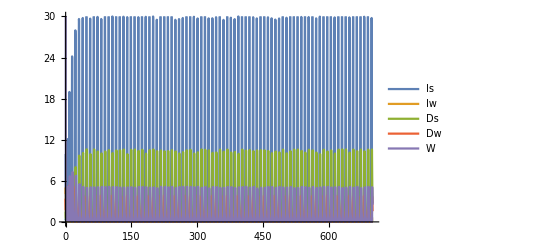

```mathematica
Plot[Evaluate[vart/.ndsol0Func1], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 30}}, PlotLegends->{"Is", "Iw", "Ds","Dw", "W"}]
```

## Mutant dynamics

```mathematica
dImudt = γm M Is  - (d + α)Imu -(Ds+Dw) (ρ+βm)Imu; (*Infected intermediate*)
dDmdt = Imu βm Ds - (μ + σ)Dm;
dMdt = fm Dm - δ M - γm Is M;
```

```mathematica
dMdt > 0
```

Dm fm-Is M γm-M δ>0

```mathematica
Am = {{-d-α - (Ds+Dw) (ρ+βm), 0, γm Is},{βm Ds, -μ -σ, 0},{0, fm, -δ- γm Is}};
Am//MatrixForm
```

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
Am.{Imu, Dm, M} == {dImudt, dDmdt, dMdt}//FullSimplify
```

True

```mathematica
FMat = {{0, 0, 0},{0, 0, 0}, {0, fm, 0}};
```

```mathematica
VMat ={{d+α+(Ds+Dw) (ρ+βm), 0, - Is γm},{-Ds βm, μ + σ, 0}, {0, 0, Is γm + δ}};
```

```mathematica
FMat - VMat == Am//FullSimplify
FMat-VMat//MatrixForm
```

True

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
R0 = Eigenvalues[FMat.Inverse[VMat]][[3]]//FullSimplify
```

(Ds fm Is βm γm)/((Is γm+δ) (d+α+(Ds+Dw) (βm+ρ)) (μ+σ))

R0=fm/(Is γm+δ)(Is  γm)/(d+α+(Ds+Dw) (ρ+βm))(Ds  βm)/(μ+σ)

# Double infections

## ODEs

-Graphics-

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
pFreeCond = {W-> 0, Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0};
pDFreeCond = { Dw-> 0, Dww-> 0};
```

## Predator and transmission functions

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]-> (ρ + βw)(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]-> (ρ + βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]-> (ρ + βw)(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]-> (ρ + βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
```

## Reproduction ratio of a resident (Existence condition for parasite)

```mathematica
MmatRes = {{-(d + αw) - Πw, 0, 0, 0, (1-p)γ Is },{0, -(d + αww)- Πww, 0, 0, p γ Is}, {βw Ds, 2(1-q)βww Ds, -(μ + σw) -(2(1-q)λww +λw), 0, 0}, {0, q βww Ds, (2(1-q)λww + λw), -(μ + σww), 0}, {0, 0, fw, fww, -δ - γ Is}};
(MmatRes/.forceInf).{Iw, Iww, Dw, Dww, W} == {dIwdt, dIwwdt, dDwdt, dDwwdt, dWdt}/.{Πw[Ds, Dw,Dww, βw]-> Πw,Πww[Ds, Dw, Dww,βww]-> Πww }/.forceInf//Simplify
```

True

```mathematica
MmatRes//MatrixForm
```

(-d-αw-Πw | 0 | 0 | 0 | Is (1-p) γ
0 | -d-αww-Πww | 0 | 0 | Is p γ
Ds βw | 2 Ds (1-q) βww | -λw-2 (1-q) λww-μ-σw | 0 | 0
0 | Ds q βww | λw+2 (1-q) λww | -μ-σww | 0
0 | 0 | fw | fww | -Is γ-δ)

```mathematica
MmatRes2 = {{-(d + αw) - Πw, 0, 0, 0, (1-p)γ Is },{0, -(d + αww)- Πww, 0, 0, p γ Is}, {βw Ds, 2(1-q)βww Ds, -(μ + σw)-(2(1-q)λww +λw) , 0, 0}, {βw Dw, q βww Ds +2(1-q)βww Dw, 0, -(μ + σww), 0}, {0, 0, fw, fww, -δ - γ Is}};
MmatRes2.{Iw, Iww, Dw, Dww, W} == {dIwdt, dIwwdt, dDwdt, dDwwdt, dWdt}/.{Πw[Ds, Dw,Dww, βw]-> Πw,Πww[Ds, Dw, Dww,βww]-> Πww }/.forceInf//Simplify
```

True

```mathematica
FmatRes = {{0, 0, 0, 0, 0},{0, 0, 0, 0, 0},{0, 0, 0, 0, 0},{0, 0, 0, 0, 0},{0, 0, fw, fww, 0}} ;
VmatRes = {{(d + αw) + Πw, 0, 0, 0, -(1-p)γ Is },{0, (d + αww)+ Πww, 0, 0, -p γ Is}, {-βw Ds, -2(1-q)βww Ds, (μ + σw) +(2(1-q)λww +λw), 0, 0}, {0,- q βww Ds, -(2(1-q)λww + λw), (μ + σww), 0}, {0, 0, 0, 0, δ + γ Is}};
FmatRes - VmatRes == MmatRes//Simplify
```

True

```mathematica
VmatRes2 = {{(d + αw) + Πw, 0, 0, 0, -(1-p)γ Is },{0, (d + αww)+ Πww, 0, 0, -p γ Is}, {-βw Ds, -2(1-q)βww Ds, (μ + σw)+(2(1-q)λww +λw) , 0, 0}, {-βw Dw, -q βww Ds -2(1-q)βww Dw, 0, (μ + σww), 0}, {0, 0, 0, 0, δ + γ Is}};
FmatRes - VmatRes2 == MmatRes2//Simplify
```

True

```mathematica
R0Res2 = Eigenvalues[FmatRes.Inverse[VmatRes2]][[5]]//Simplify;
NumR0Res2 = Numerator[R0Res2];
DenomR0Res2 = Denominator[R0Res2];
```

```mathematica
Is γ (Dw fww (λw+2 (1-q) λww+μ+σw)(2 p (1-q) βww(d +αw+ Πw)+(1-p)  βw (d +αww + Πww))  + Ds fww (λw+2 (1-q) λww+μ+σw)p q βww (d+αw+Πw)  +Ds fw  (μ+σww)(2p (1-q) βww (d+αw + Πw)+(1-p )βw(d+αww+ Πww) ))== NumR0Res2//Simplify
```

True

```mathematica
(fww/(Is γ+δ)(p γ)/(d+αww+Πww)Is(2  (1-q) βww)/(μ+σww)Dw+fww/(Is γ+δ) ((1-p)γ)/(d+αw+Πw) Is βw/(μ+σww)Dw+ fww/(Is γ+δ) (p γ)/(d+αww+Πww) Is (q βww)/(μ+σww)Ds +fw/(Is γ+δ) (p γ)/(d+αww+Πww) Is (2 (1-q) βww)/(λw+2 (1-q) λww+μ+σw)Ds + fw/(Is γ+δ) ((1-p )γ)/(d+αw+Πw) Is βw/(λw+2 (1-q) λww+μ+σw)Ds) == R0Res2//Simplify
```

True

```mathematica
fw/(Is γ+δ) ((1-p) γ)/(d+αw+Πw) Is (2 (1-q) βww)/(λw+2 (1-q) λww+μ+σw)Ds
```

(2 Ds fw Is (1-p) (1-q) βww γ)/((Is γ+δ) (d+αw+Πw) (λw+2 (1-q) λww+μ+σw))

```mathematica
FmatRes.Inverse[VmatRes2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
(Ds fw βw)/((d+αw+Πw) (λw+2 (1-q) λww+μ+σw))+(Dw fww βw)/((d+αw+Πw) (μ+σww)) | (2 Ds fw (1-q) βww)/((d+αww+Πww) (λw+2 (1-q) λww+μ+σw))-(fww (-2 Dw (1-q) βww-Ds q βww))/((d+αww+Πww) (μ+σww)) | fw/(λw+2 (1-q) λww+μ+σw) | fww/(μ+σww) | -(fw (-2 Ds Is p (1-q) βww γ (d+αw+Πw)+Ds Is (-1+p) βw γ (d+αww+Πww)))/((Is γ+δ) (d+αw+Πw) (d+αww+Πww) (λw+2 (1-q) λww+μ+σw))-(fww (Is p (-2 Dw (1-q) βww-Ds q βww) γ (d+αw+Πw)+Dw Is (-1+p) βw γ (d+αww+Πww)))/((Is γ+δ) (d+αw+Πw) (d+αww+Πww) (μ+σww)))

```mathematica
R0Res = Eigenvalues[FmatRes.Inverse[VmatRes]][[5]]//Simplify;
```

```mathematica
NumR0Res = Numerator[R0Res];
DenomR0Res = Denominator[R0Res]
```

(Is γ+δ) (d+αw+Πw) (d+αww+Πww) (λw-2 (-1+q) λww+μ+σw) (μ+σww)

```mathematica
Ds Is γ (fww ( (1-p) βw (λw+2 (1-q) λww)(d + αww + Πww)+ (p  βww 2(1-q)( λw+2  (1-q) λww) + p  βww q( λw+2  (1-q) λww+μ+σw))(αw + Πw + d))+fw (μ+σww)((1-p) (αww  + d + Πww)βw+ 2 p (1-q) (αw + d + Πw) βww  ) )==NumR0Res//Simplify
```

True

```mathematica
((λw+2 (1-q) λww)  βw)/((λw+2 (1-q) λww+μ+σw) (μ+σww))Ds fww/(Is γ+δ) ((1-p)γ)/(d+αw+Πw)Is+  (( λw+2  (1-q) λww) 2(1-q)βww)/((λw+2 (1-q) λww+μ+σw) (μ+σww))Ds fww/(Is γ+δ)(p γ)/(d+αww+Πww)Is+(q βww)/(μ + σww)Ds fww/(Is γ+δ)(p γ)/(d + αww + Πww)Is+βw/(λw+2 (1-q) λww+μ+σw)Ds fw/(Is γ+δ)(γ(1-p))/(d+αw+Πw)Is+(2  (1-q)  βww)/(λw-2 (-1+q) λww+μ+σw) Ds fw/(Is γ+δ)(γ p)/(d+αww+Πww)Is== R0Res//Simplify
```

True

```mathematica
R0freePar = R0Res/.λw-> 0/.λww-> 0//FullSimplify;
```

## Simple analytical results (linear birth functions)

Solution where both the intermediate and definitive hosts are free of parasites:

```mathematica
solRes0 = Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func0/.forceInf/.pFreeCond, varRes]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→0,Ds→0},{Is→μ/(c ρ),Ds→-(d-r)/ρ}}

Solution where infected definitive hosts do not exist (Note this solution is not biologically meaningful because I_s is always negative):

```mathematica
solResD0 =  Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func0/.forceInf/.pDFreeCond, varRes]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→0,Iw→0,Iww→0,Ds→0,W→0},{Is→-δ/γ,Iw→-((-1+p) (d-r) (d+αww) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Iww→(p (d-r) (d+αw) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Ds→0,W→-((d-r) (d+αw) (d+αww))/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ)},{Is→μ/(c ρ),Iw→0,Iww→0,Ds→(-d+r)/ρ,W→0}}

## Condition for positive parasite population (linear birth functions)

```mathematica
R0freePar/.Πw-> Πw[Ds,Dw,Dww,βw]/.Πww -> Πww[Ds,Dw,Dww,βww]/.func0/.solRes0[[2]]/.pDFreeCond;
Reduce[% > 1 && fw > 0 && fww > 0 && r > 0 && d >0 && γ > 0&&1>p>0&&1>q>0&&βw > 0 && βww > 0 &&ρ > 0 && μ >0 && σw >= 0 && σww >= 0 &&αw >= 0 && αww >=0 && c > 0 && δ > 0 && r > d, Reals]//Simplify
```

r>0&&0<d<r&&ρ>0&&βww>0&&βw>0&&αww≥0&&αw≥0&&0<q<1&&0<p<1&&σww≥0&&μ>0&&σw≥0&&c>0&&γ>-((c δ ρ (-d βw+αw ρ+r (βw+ρ)) (-d βww+αww ρ+r (βww+ρ)) (μ+σw) (μ+σww))/(μ (fw r ((-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(αw ρ+r (βw+ρ)) (μ+σw) (-fww p q r βww+(αww ρ+r (βww+ρ)) (μ+σww))+d^2 βw βww (fw (-1+p q) (μ+σww)+(μ+σw) (-fww p q+μ+σww))-d (fw (2 (-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(μ+σw) (-fww p q βww (αw ρ+r (2 βw+ρ))+(2 r βw βww+r βw ρ+αww βw ρ+r βww ρ+αw βww ρ) (μ+σww))))))&&δ>0&&((fw>((d βw-αw ρ-r (βw+ρ)) (μ+σw) (-fww p q r βww+d βww (fww p q-μ-σww)+(αww ρ+r (βww+ρ)) (μ+σww)))/((d-r) (d (-1+p q) βw βww+αww (βw-p βw) ρ-p (-1+q) r βww ρ-p (-1+q) αw βww ρ+r βw (βww-p q βww+ρ-p ρ)) (μ+σww))&&0<fww<((d βww-αww ρ-r (βww+ρ)) (μ+σww))/(p q (d-r) βww))||(fw>0&&fww≥((d βww-αww ρ-r (βww+ρ)) (μ+σww))/(p q (d-r) βww)))

```mathematica
condParasiteInv1 = {γ>-((c δ ρ (-d βw+αw ρ+r (βw+ρ)) (-d βww+αww ρ+r (βww+ρ)) (μ+σw) (μ+σww))/(μ (fw r ((-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(αw ρ+r (βw+ρ)) (μ+σw) (-fww p q r βww+(αww ρ+r (βww+ρ)) (μ+σww))+d^2 βw βww (fw (-1+p q) (μ+σww)+(μ+σw) (-fww p q+μ+σww))-d (fw (2 (-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(μ+σw) (-fww p q βww (αw ρ+r (2 βw+ρ))+(2 r βw βww+r βw ρ+αww βw ρ+r βww ρ+αw βww ρ) (μ+σww)))))), fw>((d βw-αw ρ-r (βw+ρ)) (μ+σw) (-fww p q r βww+d βww (fww p q-μ-σww)+(αww ρ+r (βww+ρ)) (μ+σww)))/((d-r) (d (-1+p q) βw βww+αww (βw-p βw) ρ-p (-1+q) r βww ρ-p (-1+q) αw βww ρ+r βw (βww-p q βww+ρ-p ρ)) (μ+σww)), fww<((d βww-αww ρ-r (βww+ρ)) (μ+σww))/(p q (d-r) βww)};
condParasiteInv2 = {γ>-((c δ ρ (-d βw+αw ρ+r (βw+ρ)) (-d βww+αww ρ+r (βww+ρ)) (μ+σw) (μ+σww))/(μ (fw r ((-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(αw ρ+r (βw+ρ)) (μ+σw) (-fww p q r βww+(αww ρ+r (βww+ρ)) (μ+σww))+d^2 βw βww (fw (-1+p q) (μ+σww)+(μ+σw) (-fww p q+μ+σww))-d (fw (2 (-1+p q) r βw βww+(-1+p) r βw ρ+(-1+p) αww βw ρ+p (-1+q) r βww ρ+p (-1+q) αw βww ρ) (μ+σww)+(μ+σw) (-fww p q βww (αw ρ+r (2 βw+ρ))+(2 r βw βww+r βw ρ+αww βw ρ+r βww ρ+αw βww ρ) (μ+σww)))))), fww>=((d βww-αww ρ-r (βww+ρ)) (μ+σww))/(p q (d-r) βww)};
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→0,Iw→0,Iww→0,Ds→0,W→0},{Is→-δ/γ,Iw→-((-1+p) (d-r) (d+αww) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Iww→(p (d-r) (d+αw) δ)/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ),Ds→0,W→-((d-r) (d+αw) (d+αww))/((d^2-p r αw+((-1+p) r+αw) αww+d (-r+αw+αww)) γ)},{Is→μ/(c ρ),Iw→0,Iww→0,Ds→(-d+r)/ρ,W→0}}

## Stability of disease free equilibrium (linear birth function)

```mathematica
Jmat = D[odesRes/.func0/.forceInf, {varRes}];
```

```mathematica
Jmat/.solRes0[[2]]/.pFreeCond//MatrixForm
eivPF = Eigenvalues[%]//FullSimplify
```

(0 | r | r | -μ/c | -μ/c | -μ/c | -(γ μ)/(c ρ)
0 | -d-αw+((d-r) (βw+ρ))/ρ | 0 | 0 | 0 | 0 | ((1-p) γ μ)/(c ρ)
0 | 0 | -d-αww+((d-r) (βww+ρ))/ρ | 0 | 0 | 0 | (p γ μ)/(c ρ)
-c (d-r) | -c (d-r)+((d-r) βw)/ρ | -c (d-r)+((d-r) βww)/ρ | 0 | μ | μ | 0
0 | -((d-r) βw)/ρ | -((1-q) (d-r) βww)/ρ | 0 | -μ-σw | 0 | 0
0 | 0 | -(q (d-r) βww)/ρ | 0 | 0 | -μ-σww | 0
0 | 0 | 0 | 0 | fw | fww | -δ-(γ μ)/(c ρ))

{-√(d-r) √μ,√(d-r) √μ,Root[1+250+#1^5&,1]/(c ρ^5),Root[1&,2]/(c ρ^5),Root[1&,3]/(c ρ^5),Root[-c^4 d^2 fw βw βww γ μ^2 ρ^22+250+#1^5&,4]/(c ρ^5),Root[-c^4 d^2 fw βw βww γ μ^2 ρ^22+250+#1^5&,5]/(c ρ^5)}
 |  |  |  |

```mathematica
Jmat/.Thread[varRes-> 0]//MatrixForm
eivExtinct = Eigenvalues[%]//FullSimplify
```

(-d+r | r | r | 0 | 0 | 0 | 0
0 | -d-αw | 0 | 0 | 0 | 0 | 0
0 | 0 | -d-αww | 0 | 0 | 0 | 0
0 | 0 | 0 | -μ | 0 | 0 | 0
0 | 0 | 0 | 0 | -μ-σw | 0 | 0
0 | 0 | 0 | 0 | 0 | -μ-σww | 0
0 | 0 | 0 | 0 | fw | fww | -δ)

{-d+r,-d-αw,-d-αww,-δ,-μ,-μ-σw,-μ-σww}

## Numerical results func0 (linear functions)

## General view

```mathematica
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

```mathematica
sys = makeSystem[varRes, vartRes, odesRes/.func0/.forceInf];
sysfunc0 = odesRes/.forceInf/.func0;
```

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};
```

{{-5.67289×10^-29,-6.30321×10^-30,5.43339×10^-30,4.94844×10^-33,-2.95824×10^-27}}

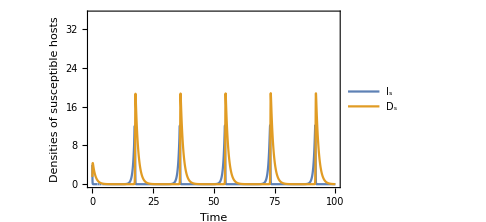
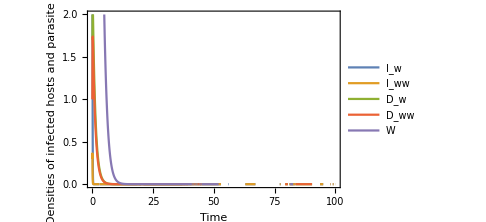
-Graphics- | -Graphics-

diseasefree_linear.jpg

```mathematica
maxt = 100;
init0= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};
sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sys/.prEco0, init0], varRes, {t, 0, maxt}] ;
p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsol0], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 35}}, PlotLegends->{"I_s",  "D_s"}, Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->Medium];
Evaluate[{Iw[maxt], Iww[maxt], Dw[maxt], Dww[maxt],W[maxt]}/.ndsol0]
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 2}},PlotLegends->{"I_w", "I_ww", "D_w", "D_ww", "W"},Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->Medium];
Grid[{{p1, p2}}]
(*Export["diseasefree_linear.jpg",%]*)
```

## Bifurcation parameter γ

```mathematica
parγ = {ρ -> 1.2, d -> 0.1,r -> 2.5, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1};;
γrange = Range[0.1, 8, 0.05];
```

```mathematica
solsγ = NSolve[Thread[(odesRes/.func0/.forceInf/.parγ/.γ-> 0.1) == 0], varRes];
```

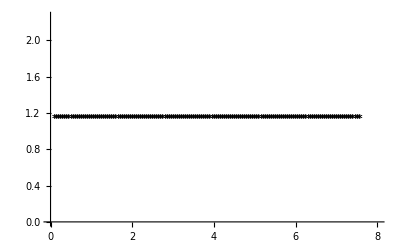

```mathematica
eqinit = {Is->1.1309523809523814,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};
eqγzero = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, eqinit];
{#}& /@Transpose[{γrange, Is/.eqγzero}];
p0 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγzero], PlotStyle-> Black];
{#}& /@Transpose[{γrange, Ds/.eqγzero}];
p1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγzero], PlotStyle-> Gray];
Show[p0, p1]
```

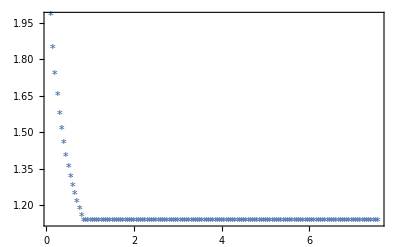

```mathematica
colordata = ColorData[97, "ColorList"];
varname = Is;
eqγ1 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[1]]];
{#}& /@Transpose[{γrange, varname/.eqγ1}];
pγ1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ1], PlotStyle-> colordata[[1]]];
eqγ2 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[2]]];
{#}& /@Transpose[{γrange, varname/.eqγ2}];
pγ2 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ2], PlotStyle-> colordata[[2]]];
eqγ13 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[13]]];
{#}& /@Transpose[{γrange, varname/.eqγ13}];
pγ13 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ13], PlotStyle-> colordata[[3]]];
eqγ16 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[16]]];
{#}& /@Transpose[{γrange, varname/.eqγ16}];
pγ16 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ16], PlotStyle-> colordata[[4]]];
eqγ17 = FollowRoot[sysfunc0, parγ, γ, γrange, varRes, solsγ[[17]]];
{#}& /@Transpose[{γrange, varname/.eqγ17}];
pγ17 = ListPlot[%, PlotMarkers->ListMark[Jmat, parγ, γ, γrange, eqγ17], PlotStyle-> colordata[[5]]];
Show[pγ1, pγ2, pγ13,pγ16,pγ17,PlotRange-> All, Frame-> True, FrameLabel-> {"Infection rate of free parasite (γ)", "Density of population"}]
```

## Bifurcation parameter βw (linear birth functions)

```mathematica
parβw = {ρ -> 1.2, d -> 0.1,r -> 2.5, γ -> 3.5, αw-> 0, αww-> 0,  βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 1.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 1.1, Κ-> 100};
βwrange = Range[1.5, 14.5, 0.1];
```

```mathematica
solsβw = NSolve[Thread[(odesRes/.func0/.forceInf/.parβw/.βw-> 1.5) == 0], varRes];
```

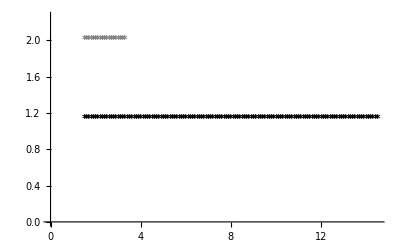

```mathematica
eqinit = {Is->1.1309523809523812,Iw->0,Iww->0,Ds->2.0000000000000004,Dw->0,Dww->0,W->0};
eqβwzero = FollowRoot[sysfunc0, parβw, βw, βwrange, varRes, eqinit];
{#}& /@Transpose[{βwrange, Is/.eqβwzero}];
p0 = ListPlot[%, PlotMarkers->ListMark[Jmat, parβw, βw, βwrange, eqβwzero], PlotStyle-> Black];
{#}& /@Transpose[{βwrange, Ds/.eqβwzero}];
p1 = ListPlot[%, PlotMarkers->ListMark[Jmat, parβw, βw, βwrange, eqβwzero], PlotStyle-> Gray];
Show[p0, p1]
```

## Stability of disease free equilibrium (nonlinear birth functions)

```mathematica
solRes1 = Solve[Thread[odesRes=={0, 0, 0, 0, 0, 0, 0}]/.func1/.forceInf/.pFreeCond, varRes]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Is→(-d+r)/(k r),Ds→0},{Is→0,Ds→0},{Is→μ/(c ρ),Ds→(-k r μ+c (-d+r) ρ)/(c ρ^2)}}

```mathematica
Reduce[(Ds/.solRes1[[3]]) > 0 && ρ > 0 && c > 0 && d  > 0 && μ > 0 && r > 0 && k >0, k, Reals]
```

c>0&&r>0&&0<d<r&&μ>0&&ρ>0&&0<k<(-c d ρ+c r ρ)/(r μ)

```mathematica
Jmat = D[odesRes/.func1/.forceInf, {varRes}];
```

```mathematica
Jmat/.pFreeCond;
eivPF = Eigenvalues[%]/.solRes1[[3]]
```

{1/2 (-d+r-(2 k r μ)/(c ρ)-(-k r μ+c (-d+r) ρ)/(c ρ)-√(-(4 μ (-k r μ+c (-d+r) ρ))/(c ρ)+(d-r+(2 k r μ)/(c ρ)+(-k r μ+c (-d+r) ρ)/(c ρ))^2)),1/2 (-d+r-1/1-1/(c ρ)+√(-1/(c ρ)+(1)^2)),3,1,Root[r^2 δ μ^2+r αw δ μ^2+r αww δ μ^2+540+(2 r+αw+αww+δ+2 μ-(k r βw μ)/(c ρ^2)-(k r βww μ)/(c ρ^2)-(d βw)/ρ+(r βw)/ρ-(d βww)/ρ+(r βww)/ρ-(2 k r μ)/(c ρ)+(γ μ)/(c ρ)+σw+σww) #1^4+#1^5&,5]}
 |  |  |  |

```mathematica
Simplify[Reduce[eivPF[[1]]<0 &&eivPF[[2]]<0   && ρ > 0&&d > 0 && c > 0 && k > 0 && r > 0 && r > d && μ > 0 ,   k], c > 0 && r > 0 && ρ > 0 && μ > 0]
condPfreeStableNL = %[[2]]
```

0<d<r&&(2 c (-1+√((-d+r+μ)/μ)) ρ)/r≤k<(c (-d+r) ρ)/(r μ)

(2 c (-1+√((-d+r+μ)/μ)) ρ)/r≤k<(c (-d+r) ρ)/(r μ)

```mathematica
Reduce[condPfreeStableNL[[1]] < condPfreeStableNL[[3]] && c > 0 && r > 0 && ρ > 0 && μ > 0 && r > d]
```

ρ>0&&r>0&&k>0&&c>0&&d<r&&μ>(-4 c^2 d ρ^2+4 c^2 r ρ^2)/(k^2 r^2+4 c k r ρ)

## Condition for positive parasite population (nonlinear birth functions)

```mathematica
R0freePar/.{αw -> α, αww -> α}/.{σw -> σ, σww -> σ}/.{fww-> f, fw-> f}
```

(Ds Is γ (f p q βww (α+Πw) (μ+σ)-f ((-1+p) α βw+2 p (-1+q) βww (α+Πw)+(-1+p) βw Πww) (μ+σ)+d (f p q βww (μ+σ)-f ((-1+p) βw+2 p (-1+q) βww) (μ+σ))))/((Is γ+δ) (d+α+Πw) (d+α+Πww) (μ+σ)^2)

```mathematica
R0freePar/.{αw -> α, αww -> α}/.{σw -> σ, σww -> σ}/.{fww-> f, fw-> f}/.Πw-> Πw[Ds,Dw,Dww,βw]/.Πww -> Πww[Ds,Dw,Dww,βww]/.func1/.solRes1[[3]]/.pFreeCond//FullSimplify;
condPspreadNL = Reduce[% > 1 && 1>p> 0 && 1>q>0 && k<(c (-d+r) ρ)/(r μ)&&f > 0 && r > d && γ > 0 && c > 0 && d > 0 && βw >0&&βww>0&& r > 0 && d > 0 && δ > 0 && α >= 0 && μ>0 && ρ > 0 &&σ >= 0];
condPspreadNL [[15]]//FullSimplify
```

0<δ<-((γ μ (f (k r μ+c (d-r) ρ) (k r μ ((-1+p (-1+q)) βw βww+(-1+p) βw ρ+p (-2+q) βww ρ)+c ρ ((-1+p (-1+q)) (d-r) βw βww-(r+α) ((-1+p) βw+p (-2+q) βww) ρ))+(k r μ (βw+ρ)-c ρ (-d βw+r βw+(r+α) ρ)) (k r μ (βww+ρ)-c ρ (-d βww+r βww+(r+α) ρ)) (μ+σ)))/(c ρ (-k r μ (βw+ρ)+c ρ (-d βw+r βw+(r+α) ρ)) (-k r μ (βww+ρ)+c ρ (-d βww+r βww+(r+α) ρ)) (μ+σ)))

```mathematica
AbsoluteTiming[Reduce[(R0freePar/.Πw-> Πw[Ds,Dw,Dww,βw]/.Πww -> Πww[Ds,Dw,Dww,βww]/.func1/.pFreeCond) > 1 && 1>p> 0 && 1>q>0]]
```

$Aborted

## Numerical analysis (non-linear birth function)

```mathematica
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
sys = makeSystem[varRes, vartRes, odesRes/.func1/.forceInf];
```

## Disease-free equilibrium

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9, k -> 0.26};
```

```mathematica
condPfreeStableNL/.prEcoNL
```

True

{{2.32143,0.0758929}}

{{-1.07503×10^-16,-1.19448×10^-17,8.08519×10^-18,7.36356×10^-21,1.32459×10^-16}}

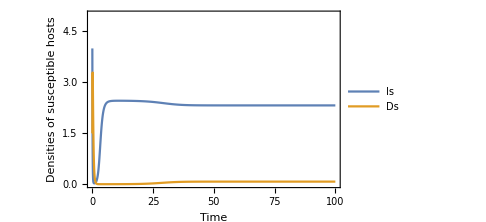
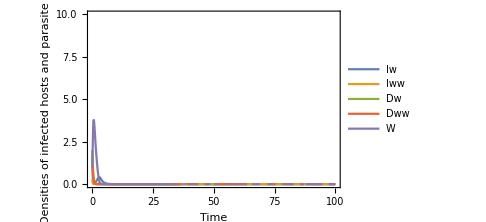
-Graphics- | -Graphics-

Diseasefree.jpeg

```mathematica
maxt = 100;
initNL= {Is[0]== 4, Iw[0] == 2,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 1};
solsNL = NSolve[Thread[(odesRes/.func1/.forceInf/.prEcoNL) == 0], varRes];
ndsolNL = NDSolve[Join[sys/.prEcoNL, initNL], varRes, {t, 0, maxt}] ;
p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->Medium];
Evaluate[{Is[maxt], Ds[maxt]}/.ndsolNL]
Evaluate[{Iw[maxt], Iww[maxt], Dw[maxt], Dww[maxt],W[maxt]}/.ndsolNL]
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolNL], {t, 0, maxt}, PlotRange->{{0, maxt},{0, 10}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->Medium];
Grid[{{p1, p2}}]
(*Export["Diseasefree.jpeg",%]*)
```

## Disease-stable equilibrium

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, f -> 40.5, δ-> 0.9, k -> 0.26};
```

```mathematica
condPspreadNL/.prEcoDSNL/.α-> 0/.σ -> 0
```

True

```mathematica
solsNL[[20]]
```

{Is→2.32143,Iw→0,Iww→0,Ds→0.0758929,Dw→0,Dww→0,W→0}

```mathematica
Eigenvalues[Jmat/.condsimplifyNL/.solsNL[[19]]/.prEcoDSNL]
```

{-6.33279+1.66267 ⅈ,-6.33279-1.66267 ⅈ,-3.9+0. ⅈ,-1.21711+0. ⅈ,-1.10491+0. ⅈ,-0.291822+0. ⅈ,0.0285344+0. ⅈ}

```mathematica
Eigenvalues[Jmat/.condsimplifyNL/.solsNL[[20]]/.prEcoDSNL]
```

{-6.2573+1.7295 ⅈ,-6.2573-1.7295 ⅈ,-4.04339+0. ⅈ,-1.19842+0. ⅈ,-1.10607+0. ⅈ,-0.307402+0. ⅈ,-0.0299051+0. ⅈ}

```mathematica
condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ, fw-> f, fww-> f};
```

```mathematica
sys
```

{Is'[t]==-d Is[t]-ρ (Ds[t]+Dw[t]+Dww[t]) Is[t]+r (Is[t]+Iw[t]+Iww[t]) (1-k (Is[t]+Iw[t]+Iww[t]))-γ Is[t] W[t],Iw'[t]==-((d+αw) Iw[t])-(βw+ρ) (Ds[t]+Dw[t]+Dww[t]) Iw[t]+(1-p) γ Is[t] W[t],Iww'[t]==-((d+αww) Iww[t])-(βww+ρ) (Ds[t]+Dw[t]+Dww[t]) Iww[t]+p γ Is[t] W[t],Ds'[t]==-μ Ds[t]+c ρ (Ds[t]+Dw[t]+Dww[t]) (Is[t]+Iw[t]+Iww[t])-Ds[t] (βw Iw[t]+βww Iww[t]),Dw'[t]==-((μ+σw) Dw[t])+Ds[t] (βw Iw[t]+2 (1-q) βww Iww[t])-Dw[t] (βw Iw[t]+2 (1-q) βww Iww[t]),Dww'[t]==-((μ+σww) Dww[t])+q βww Ds[t] Iww[t]+Dw[t] (βw Iw[t]+2 (1-q) βww Iww[t]),W'[t]==fw Dw[t]+fww Dww[t]-δ W[t]-γ Is[t] W[t]}

{{Is→InterpolatingFunction[…],Iw→InterpolatingFunction[…],Iww→InterpolatingFunction[…],Ds→InterpolatingFunction[…],Dw→InterpolatingFunction[…],Dww→InterpolatingFunction[…],W→InterpolatingFunction[…]}}

{{2.45037,3.8325×10^-8}}

{{0.00850608,0.00094512,1.83047×10^-10,1.38472×10^-12,1.26011×10^-9}}

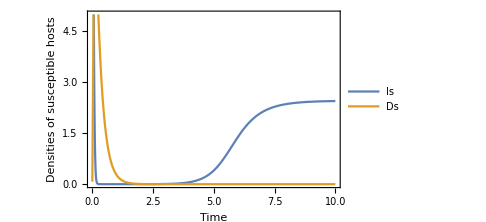
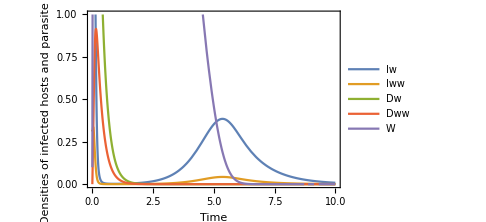
-Graphics- | -Graphics-

```mathematica
maxt = 10;
{(*Is[0]== 17.6, Iw[0] == 1.2,Iww[0]==0.32, Ds[0] ==3.4, Dw[0] == 1.7,Dww[0]==0.1, W[0] == 0.1*)Is[0]== 17.6, Iw[0] == 1.2,Iww[0]==0.32, Ds[0] ==0.07361487073332167, Dw[0] == 3,Dww[0]==0.000098445034304292, W[0] == 0.1};
ndsolNL = NDSolve[Join[sys/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt},WorkingPrecision->MachinePrecision] 
solsNL = NSolve[Thread[(odesRes/.condsimplifyNL/.func1/.forceInf/.prEcoDSNL) == 0], varRes];
p1 = Plot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 5}}, PlotLegends->{"Is",  "Ds"},Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of susceptible hosts"}, ImageSize->Medium];
Evaluate[{Is[maxt], Ds[maxt]}/.ndsolNL]
Evaluate[{Iw[maxt], Iww[maxt], Dw[maxt], Dww[maxt],W[maxt]}/.ndsolNL]
p2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsolNL], {t, 0, maxt}, PlotRange->{{0, maxt
},{0, 1}},PlotLegends->{"Iw", "Iww", "Dw", "Dww", "W"}, Frame-> {True, True, False, False}, FrameLabel->{"Time", "Densities of infected hosts and parasite pool"}, ImageSize->Medium];
Grid[{{p1, p2}}]
```

```mathematica
solsNL[[20]]
```

{Is→2.22695,Iw→0.0783541,Iww→0.00870601,Ds→0.0736149,Dw→0.00261056,Dww→0.000098445,W→0.0149106}

```mathematica
solsNL//MatrixForm
```

(Is→-0.00282967 | Iw→-2.22624 | Iww→-0.24736 | Ds→-26.102 | Dw→-611.077 | Dww→638.369 | W→1239.42
Is→-0.00282967 | Iw→-2.22624 | Iww→-0.24736 | Ds→-26.102 | Dw→-611.077 | Dww→638.369 | W→1239.42
Is→-0.00282967 | Iw→-2.22624 | Iww→-0.24736 | Ds→-26.102 | Dw→-611.077 | Dww→638.369 | W→1239.42
Is→-0.00282967 | Iw→-2.22624 | Iww→-0.24736 | Ds→-26.102 | Dw→-611.077 | Dww→638.369 | W→1239.42
Is→-0.00282967 | Iw→-2.22624 | Iww→-0.24736 | Ds→-26.102 | Dw→-611.077 | Dww→638.369 | W→1239.42
Is→8.75888 | Iw→-6.08326 | Iww→-0.675918 | Ds→0.0417686 | Dw→0.064292 | Dww→-0.183627 | W→-0.183762
Is→8.75888 | Iw→-6.08326 | Iww→-0.675918 | Ds→0.0417686 | Dw→0.064292 | Dww→-0.183627 | W→-0.183762
Is→0 | Iw→6.42741 | Iww→-2.58125 | Ds→-0.222753 | Dw→-0.0748775 | Dww→-0.0357032 | W→-4.97613
Is→0 | Iw→6.42741 | Iww→-2.58125 | Ds→-0.222753 | Dw→-0.0748775 | Dww→-0.0357032 | W→-4.97613
Is→-0.310345 | Iw→2.49469 | Iww→0.277188 | Ds→0 | Dw→0 | Dww→0 | W→-2.77188
Is→2.52813 | Iw→-3.878 | Iww→1.94875 | Ds→-0.333333 | Dw→0.00251726 | Dww→-0.00251726 | W→0
Is→3.0804 | Iw→-0.607876 | Iww→-0.0675418 | Ds→0.0660647 | Dw→-0.0263637 | Dww→0.00750267 | W→-0.0776832
Is→3.0804 | Iw→-0.607876 | Iww→-0.0675418 | Ds→0.0660647 | Dw→-0.0263637 | Dww→0.00750267 | W→-0.0776832
Is→2.61564 | Iw→-2.34141 | Iww→-0.260157 | Ds→0.0577946 | Dw→0.643571 | Dww→-0.707126 | W→-0.303342
Is→2.61564 | Iw→-2.34141 | Iww→-0.260157 | Ds→0.0577946 | Dw→0.643571 | Dww→-0.707126 | W→-0.303342
Is→-0.524055 | Iw→2.46005 | Iww→0.273339 | Ds→0.0248898 | Dw→0.0133364 | Dww→0.0154208 | W→-1.87923
Is→-0.524055 | Iw→2.46005 | Iww→0.273339 | Ds→0.0248898 | Dw→0.0133364 | Dww→0.0154208 | W→-1.87923
Is→2.46154 | Iw→0 | Iww→0 | Ds→0 | Dw→0 | Dww→0 | W→0
Is→2.32143 | Iw→0 | Iww→0 | Ds→0.0758929 | Dw→0 | Dww→0 | W→0
Is→2.22695 | Iw→0.0783541 | Iww→0.00870601 | Ds→0.0736149 | Dw→0.00261056 | Dww→0.000098445 | W→0.0149106
Is→2.19925 | Iw→2.29219 | Iww→-1.15185 | Ds→-0.333333 | Dw→-0.00147022 | Dww→0.00147022 | W→0
Is→2.19925 | Iw→2.29219 | Iww→-1.15185 | Ds→-0.333333 | Dw→-0.00147022 | Dww→0.00147022 | W→0
Is→2.19925 | Iw→2.29219 | Iww→-1.15185 | Ds→-0.333333 | Dw→-0.00147022 | Dww→0.00147022 | W→0
Is→2.19925 | Iw→2.29219 | Iww→-1.15185 | Ds→-0.333333 | Dw→-0.00147022 | Dww→0.00147022 | W→0
Is→2.19925 | Iw→2.29219 | Iww→-1.15185 | Ds→-0.333333 | Dw→-0.00147022 | Dww→0.00147022 | W→0
Is→2.19925 | Iw→2.29219 | Iww→-1.15185 | Ds→-0.333333 | Dw→-0.00147022 | Dww→0.00147022 | W→0
Is→-0.310345 | Iw→0.27931 | Iww→0.0310345 | Ds→0 | Dw→0 | Dww→0 | W→-0.310345
Is→0 | Iw→0 | Iww→0 | Ds→0 | Dw→0 | Dww→0 | W→0)

```mathematica
Sign[Eigenvalues[Jmat/.condsimplifyNL/.solsNL[[1]]/.prEcoDSNL]⟦1⟧]
```

-1.+0. ⅈ

```mathematica
Table[Eigenvalues[Jmat/.condsimplifyNL/.solsNL[[i]]/.prEcoDSNL],{i,Length[solsNL]}]//Sign//MatrixForm
```

(-1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.227953+0.973672 ⅈ | 0.227953-0.973672 ⅈ | -1.+0. ⅈ | 1.+0. ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.227953+0.973672 ⅈ | 0.227953-0.973672 ⅈ | -1.+0. ⅈ | 1.+0. ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.227953+0.973672 ⅈ | 0.227953-0.973672 ⅈ | -1.+0. ⅈ | 1.+0. ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.227953+0.973672 ⅈ | 0.227953-0.973672 ⅈ | -1.+0. ⅈ | 1.+0. ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.227953+0.973672 ⅈ | 0.227953-0.973672 ⅈ | -1.+0. ⅈ | 1.+0. ⅈ
-1.+0. ⅈ | 1.+0. ⅈ | 1.+0. ⅈ | -1.+0. ⅈ | -0.199389+0.97992 ⅈ | -0.199389-0.97992 ⅈ | -1.+0. ⅈ
-1.+0. ⅈ | 1.+0. ⅈ | 1.+0. ⅈ | -1.+0. ⅈ | -0.199389+0.97992 ⅈ | -0.199389-0.97992 ⅈ | -1.+0. ⅈ
1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.466894+0.884313 ⅈ | 0.466894-0.884313 ⅈ | -1.+0. ⅈ
1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.466894+0.884313 ⅈ | 0.466894-0.884313 ⅈ | -1.+0. ⅈ
-1 | -1 | 1 | -1 | -1 | -1 | 1
-1.+0. ⅈ | -0.200541+0.979685 ⅈ | -0.200541-0.979685 ⅈ | -1.+0. ⅈ | 0.808299+0.588773 ⅈ | 0.808299-0.588773 ⅈ | -1.+0. ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.408151+0.912914 ⅈ | 0.408151-0.912914 ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 0.408151+0.912914 ⅈ | 0.408151-0.912914 ⅈ
-1 | -1 | -1 | 1 | 1 | -1 | 1
-1 | -1 | -1 | 1 | 1 | -1 | 1
-1.+0. ⅈ | -1.+0. ⅈ | 1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -0.841302+0.540566 ⅈ | -0.841302-0.540566 ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | 1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -0.841302+0.540566 ⅈ | -0.841302-0.540566 ⅈ
-1 | -1 | -1 | -1 | -1 | -1 | 1
-0.967219+0.253943 ⅈ | -0.967219-0.253943 ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | 1.+0. ⅈ
-0.96386+0.266408 ⅈ | -0.96386-0.266408 ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ | -1.+0. ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -0.185931+0.982563 ⅈ | -0.185931-0.982563 ⅈ | -1.+0. ⅈ | 0.431318+0.9022 ⅈ | 0.431318-0.9022 ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -0.185931+0.982563 ⅈ | -0.185931-0.982563 ⅈ | -1.+0. ⅈ | 0.431318+0.9022 ⅈ | 0.431318-0.9022 ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -0.185931+0.982563 ⅈ | -0.185931-0.982563 ⅈ | -1.+0. ⅈ | 0.431318+0.9022 ⅈ | 0.431318-0.9022 ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -0.185931+0.982563 ⅈ | -0.185931-0.982563 ⅈ | -1.+0. ⅈ | 0.431318+0.9022 ⅈ | 0.431318-0.9022 ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -0.185931+0.982563 ⅈ | -0.185931-0.982563 ⅈ | -1.+0. ⅈ | 0.431318+0.9022 ⅈ | 0.431318-0.9022 ⅈ
-1.+0. ⅈ | -1.+0. ⅈ | -0.185931+0.982563 ⅈ | -0.185931-0.982563 ⅈ | -1.+0. ⅈ | 0.431318+0.9022 ⅈ | 0.431318-0.9022 ⅈ
-1 | -1 | -1 | 1 | 1 | -1 | -1
-1 | -1 | -1 | 1 | -1 | -1 | -1)

## Mutant dynamics

```mathematica
2p (M W)/(M + W)^2+ p M^2/(M+W)^2+(1-p)W/(M + W)+(1-p)M/(M+W)+p W^2/(M + W)^2//FullSimplify
```

1

```mathematica
dImdt = (1-p)ηm Is - (d + αm) Imut - Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw]Imut;
dImmdt = p ηmm Is - (d + αmm) Imm - Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw]Imm;
dImwdt = p ηmw Is - (d + αmw) Imw - Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw]Imw;
dDmdt =( λm + (1-q)(λmm + λmw))Ds - (μ + σm) Dm - (λw + λm+ (1-q)(λww + λmw+λmm) )Dm;
dDmmdt = q λmm Ds + (λm + (1-q)(λmm + λmw))Dm -(μ + σmm)Dmm;
dDmwdt = q λmw Ds + (λm + (1-q)(λmm + λmw))Dw + (λw + (1-q)(λww + λmw))Dm - (μ + σmw) Dmw;
dMdt = fm Dm + fmm Dmm + fmw Dmw - δ M - (ηm + ηmw + ηmm)Is;
odesMut = {dImdt, dImmdt, dImwdt, dDmdt, dDmmdt, dDmwdt, dMdt};
varMut = {Imut,  Imm,Imw, Dm, Dmm, Dmw, M};
forceInfMut = {ηm -> γ M/(M+W)(M + W), ηmm ->γ M^2/(M+W)^2(M + W), ηmw ->  γ 2 (M W)/(M + W)^2(M + W), λm -> βm Imut, λmw -> βmw Imw, λmm -> βmm Imm, λw -> βw Iw, λww -> βww Iww};
```

```mathematica
Mmat ={ {- (d + αm)- Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw], 0, 0, 0, 0, 0, (1-p)γ Is},
{0, - (d + αmm)- Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw], 0, 0, 0, 0, p γ M/(M+W)Is}, {0, 0, - (d + αmw) - Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw], 0, 0, 0, p γ 2 W/(M + W)Is}, {βm Ds, (1-q)βmm Ds, (1-q)βmw Ds, - (μ + σm)- (λw + λm+ (1-q)(λww + λmw+λmm) ), 0, 0, 0}, {0, q βmm Ds, 0, (λm + (1-q)(λmm + λmw)),  -(μ + σmm), 0, 0}, {βm Dw, (1-q)βmm Dw, q βmw Ds + (1-q)βmw Dw, (λw + (1-q)(λww + λmw)), 0,- (μ + σmw) , 0 }, {0, 0, 0, fm, fmm, fmw, -δ -(1 + 2 W/(M+W)+M/(M+W))γ Is}};
```

```mathematica
((Mmat.varMut)/.forceInfMut)==(odesMut/.forceInfMut)//Simplify
```

True

```mathematica
Mmat//MatrixForm
```

(-d-αm-Πm[Ds,Dw,Dww,βm,Dm,Dmm,Dmw] | 0 | 0 | 0 | 0 | 0 | Is (1-p) γ
0 | -d-αmm-Πmm[Ds,Dw,Dww,βmm,Dm,Dmm,Dmw] | 0 | 0 | 0 | 0 | (Is M p γ)/(M+W)
0 | 0 | -d-αmw-Πmw[Ds,Dw,Dww,βmw,Dm,Dmm,Dmw] | 0 | 0 | 0 | (2 Is p W γ)/(M+W)
Ds βm | Ds (1-q) βmm | Ds (1-q) βmw | -λm-λw-(1-q) (λmm+λmw+λww)-μ-σm | 0 | 0 | 0
0 | Ds q βmm | 0 | λm+(1-q) (λmm+λmw) | -μ-σmm | 0 | 0
Dw βm | Dw (1-q) βmm | Dw (1-q) βmw+Ds q βmw | λw+(1-q) (λmw+λww) | 0 | -μ-σmw | 0
0 | 0 | 0 | fm | fmm | fmw | -Is (1+M/(M+W)+(2 W)/(M+W)) γ-δ)

```mathematica
Fmat = { {0, 0, 0, 0, 0, 0, 0},
{0, 0, 0, 0, 0, 0,0}, {0, 0, 0, 0, 0, 0,0}, {0, 0, 0,0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0,0 , 0, 0 }, {0, 0, 0, fm, fmm, fmw, 0}};
```

```mathematica
Vmat = { { (d + αm)+ Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw], 0, 0, 0, 0, 0, -(1-p)γ Is},
{0,  (d + αmm)+ Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw], 0, 0, 0, 0, -p γ M/(M+W)Is}, {0, 0,  (d + αmw) + Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw], 0, 0, 0,- p γ 2 W/(M + W)Is}, {-βm Ds, -(1-q)βmm Ds, -(1-q)βmw Ds,  (μ + σm)+(λw + λm+ (1-q)(λww + λmw+λmm) ), 0, 0, 0}, {0,- q βmm Ds, 0, -(λm + (1-q)(λmm + λmw)),  (μ + σmm), 0, 0}, {-βm Dw, -(1-q)βmm Dw,- q βmw Ds - (1-q)βmw Dw, -(λw + (1-q)(λww + λmw)), 0, (μ + σmw) , 0 }, {0, 0, 0, 0, 0, 0, δ +(1 + 2 W/(M+W)+M/(M+W))γ Is}};
```

```mathematica
Vmat[[1]][[7]]
```

Is (-1+p) γ

```mathematica
Fmat - Vmat == Mmat//FullSimplify
```

True

```mathematica
varMut
```

{Imut,Imm,Imw,Dm,Dmm,Dmw,M}

```mathematica
Fmat.Inverse[Vmat]/.Πmm[Ds,Dw,Dww,βmm,Dm,Dmm,Dmw]-> Πmm/.Πm[Ds,Dw,Dww,βm,Dm,Dmm,Dmw]-> Πm/.Πmw[Ds,Dw,Dww,βmw,Dm,Dmm,Dmw]-> Πmw/.λm-> 0/.λmm-> 0/.λmw-> 0/.Is (1+M/(M+W)+(2 W)/(M+W))->Is( 1+freqM+2 freqW)/.M+W-> ET//Simplify
Eigenvalues[%][[7]]
```

```mathematica
R0 = Eigenvalues[(Fmat.Inverse[Vmat])/.forceInfMut/. Πm[Ds, Dw,Dww, βm, Dm, Dmm, Dmw]-> Πm/.Πmm[Ds, Dw,Dww, βmm, Dm, Dmm, Dmw]-> Πmm/. Πmw[Ds, Dw,Dww, βmw, Dm, Dmm, Dmw]-> Πmw][[7]]/.M-> 0/. Imut-> 0/.Imw -> 0/.Imm-> 0//Simplify;
```

```mathematica
forceInfMut
```

{ηm→M γ,ηmm→(M^2 γ)/(M+W),ηmw→(2 M W γ)/(M+W),λm→Imut βm,λmw→Imw βmw,λmm→Imm βmm,λw→Iw βw,λww→Iww βww}

```mathematica
NumR0 = Numerator[Simplify[R0]];
DenR0 = Denominator[Simplify[R0]];
```

```mathematica
{Is γ (Dw fmw XX((1-p)βm (d+αmw + Πmw)+  2p(1-q) (d+ αm+Πm) βmw ) +Ds fmw (YY(1-p) βm(αmw+Πmw+d)+2 p βmw( Πm+αm+d)(YY+q (μ+σm)) )+Ds fm  (μ+σmw)((1-p) (d+ αmw+Πmw) βm+ 2p (1-q) (d+αm+ Πm) βmw) )/.XX-> (Iw βw+Iww (βww-q βww)+μ+σm)/.YY -> (Iw βw + Iww (βww-q βww))}=={NumR0}//FullSimplify
```

True

```mathematica
fmw/(3 Is γ+δ)((1-p) γ)/(d+αm+Πm)Is(βm/(μ+σmw)Dw+(βm ( βw Iw +  (1-q) βww Iww))/((βw Iw +  (1-q) βww Iww+μ+σm) (μ+σmw))Ds)+fmw/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is(((1-q) βmw)/(μ+σmw)Dw +((1-q)βmw  (Iw βw +  (1-q)βww Iww))/((βw Iw +  (1-q) βww Iww+μ+σm) (μ+σmw))Ds+(q βmw)/(μ+σmw)Ds)+fm/(3 Is γ+δ)γ/(d+αm+Πm)Is((1-p)  βm Ds)/(Iw βw+Iww (βww-q βww)+μ+σm)+fm/(3 Is γ+δ)(p Is γ)/(d+αmw+Πmw)(Ds  2(1-q)  βmw)/(Iw βw+Iww (βww-q βww)+μ+σm)==NumR0/DenR0//FullSimplify
```

True

Different routes of propagation of a mutant

R_(mix1=)fmw/(3 Is γ+δ)((1-p) γ)/(d+αm+Πm)Is βm/(μ+σmw)Dw-> mutants born from mixed infected D hosts (D_mw), singly infect I hosts and infect a wild-type infected D hosts (mutant comes after wild type in D host).

R_mix2 = fmw/(3 Is γ+δ)((1-p) γ)/(d+αm+Πm)Is(βm ( βw Iw +  (1-q) βww Iww))/((Iw βw+Iww (βww-q βww)+μ+σm) (μ+σmw)) Ds-> mutants born from mixed infected D hosts (D_mw),
singly infect I hosts, singly infect  D hosts and then sequentialy infected by a wild type (mutant comes before the wild type in D host)

R_mix3 = fmw/(3 Is γ+δ)(2p  γ)/(d+αmw+Πmw)Is(q βmw)/(μ+σmw)Ds-> mutants born from mixed infected D hosts (D_mw), cotransmit with wild type in I hosts and cotransmit with wild type in D hosts (mutant comes with wild type in D host)
 
R_mix4 =  fmw/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is((1-q) βmw)/(μ+σmw)Dw -> mutants born from mixed infected D hosts (D_mw), cotransmit with wild type in I hosts, and infects a wild-type infected D hosts (mutant comes after wild type in D host)

R_mix5 = fmw/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is((1-q)βmw  (Iw βw +  (1-q)βww Iww))/((βw Iw +  (1-q) βww Iww+μ+σm) (μ+σmw))Ds -> mutants born from mixed infected D hosts (D_mw), cotransmit with wild type in I hosts, singly infects D host and sequentially infected by wild type (mutant comes before wild type in D host) 

R_s1 =  fm/(3 Is γ+δ)((1-p)γ)/(d+αm+Πm)Is βm/(Iw βw+Iww (βww-q βww)+μ+σm)Ds -> mutants born from singly infected D hosts (D_m), singly infect I hosts, and then singly infect D hosts

R_s2 = fm/(3 Is γ+δ)(2 p  γ)/(d+αmw+Πmw)Is((1-q)  βmw)/(Iw βw+Iww (βww-q βww)+μ+σm)Ds-> mutants born from singly infected D hosts (D_m), cotransmit with wild type in I hosts, singly infected D hosts and then singly infect a D host

True